```mathematica
{hmugen1,hmugen10,hmugen50,hmugen90,hmugen99,hmukeep1,hmukeep10,hmukeep50,hmukeep90,hmukeep99,hmumem1,hmumem10,hmumem50,hmumem90,hmumem99,hmukill1,hmukill10,hmukill50,hmukill90,hmukill99,hmutyp1,hmutyp10,hmutyp50,hmutyp90,hmutyp99}=Import["C:\\Users\\muxy1\\OneDrive\\桌面\\Modeling paper\\hmu500c24hpercent.mx"];
```

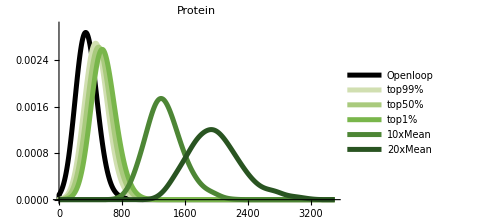

```mathematica
SmoothHistogram[{ol500c24h[[1]][[1]]/ol500c24h[[1]][[6]],hmugen1[[1]][[1]]/hmugen1[[1]][[6]],hmugen50[[1]][[1]]/hmugen50[[1]][[6]],hmugen99[[1]][[1]]/hmugen99[[1]][[6]],hmugen7000[[1]][[1]]/hmugen7000[[1]][[6]],hmugen14000[[1]][[1]]/hmugen14000[[1]][[6]]},100,PlotRange->{{0,3500},{0,0.003}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Protein",Black,16],PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#d1dfb1"],Thickness[0.01]],Directive[RGBColor["#a9ca7d"],Thickness[0.01]],Directive[RGBColor["#79b64b"],Thickness[0.01]],Directive[RGBColor["#4d8635"],Thickness[0.01]],Directive[RGBColor["#295421"],Thickness[0.01]]},AxesStyle->Directive[Black, 14],ImageSize->Medium]
```

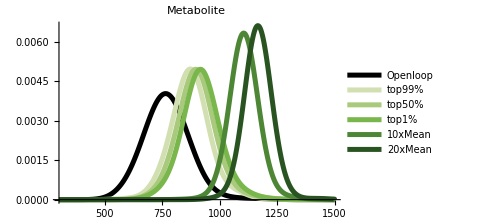

```mathematica
SmoothHistogram[{ol500c24h[[1]][[4]]/ol500c24h[[1]][[6]],hmugen1[[1]][[4]]/hmugen1[[1]][[6]],hmugen50[[1]][[4]]/hmugen50[[1]][[6]],hmugen99[[1]][[4]]/hmugen99[[1]][[6]],hmugen7000[[1]][[4]]/hmugen7000[[1]][[6]],hmugen14000[[1]][[4]]/hmugen14000[[1]][[6]]},50,PlotRange->{{300,1500},Automatic},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Metabolite",Black,16],PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#d1dfb1"],Thickness[0.01]],Directive[RGBColor["#a9ca7d"],Thickness[0.01]],Directive[RGBColor["#79b64b"],Thickness[0.01]],Directive[RGBColor["#4d8635"],Thickness[0.01]],Directive[RGBColor["#295421"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

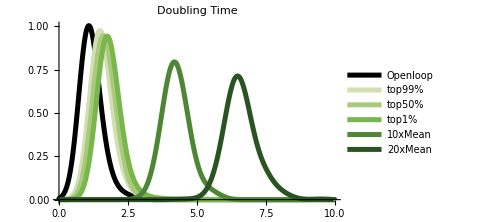

```mathematica
SmoothHistogram[{Log[2]/ol500c24h[[1]][[5]],Log[2]/hmugen1[[1]][[5]],Log[2]/hmugen50[[1]][[5]],Log[2]/hmugen99[[1]][[5]],Log[2]/hmugen7000[[1]][[5]],Log[2]/hmugen14000[[1]][[5]]},0.3,PlotRange->{{0,10},Automatic},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Doubling Time",Black,16],PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#d1dfb1"],Thickness[0.01]],Directive[RGBColor["#a9ca7d"],Thickness[0.01]],Directive[RGBColor["#79b64b"],Thickness[0.01]],Directive[RGBColor["#4d8635"],Thickness[0.01]],Directive[RGBColor["#295421"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
hmumem7000=metabproteinmemfast[hmukeep7000];
```

```mathematica
hmumem14000=metabproteinmemfast[hmukeep14000];
```

```mathematica
{hmumem1,hmumem50,hmumem99,hmumem7000,hmumem14000}=Parallelize[{metabproteinmemfast[hmukeep1],metabproteinmemfast[hmukeep50],metabproteinmemfast[hmukeep99],metabproteinmemfast[hmukeep7000],metabproteinmemfast[hmukeep14000]}];
```

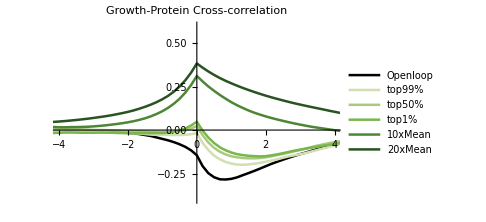

```mathematica
ListLinePlot[{ol500c24hmem[[4]],hmumem1[[4]],hmumem50[[4]],hmumem99[[4]],hmumem7000[[4]],hmumem14000[[4]]},PlotRange->{{-4,4},{-0.4,0.6}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Growth-Protein Cross-correlation",Black,16],PlotStyle->{Directive[Black,Thickness[0.005]],Directive[RGBColor["#d1dfb1"],Thickness[0.005]],Directive[RGBColor["#a9ca7d"],Thickness[0.005]],Directive[RGBColor["#79b64b"],Thickness[0.005]],Directive[RGBColor["#4d8635"],Thickness[0.005]],Directive[RGBColor["#295421"],Thickness[0.005]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

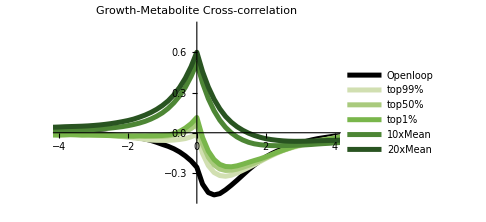

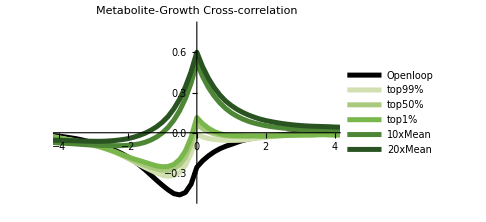

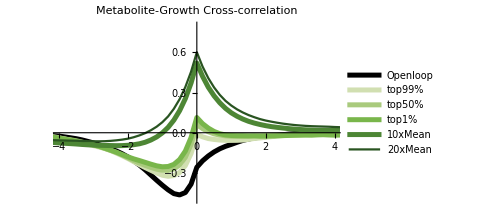

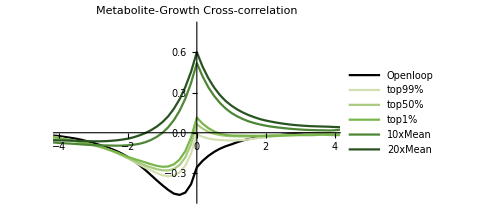

```mathematica
ListLinePlot[{ol500c24hmem[[5]],hmumem1[[5]],hmumem50[[5]],hmumem99[[5]],hmumem7000[[5]],hmumem14000[[5]]},PlotRange->{{-4,4},{-0.5,0.8}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Growth-Metabolite Cross-correlation",Black,16],PlotStyle->{Directive[Black,Thickness[0.01]],Directive[RGBColor["#d1dfb1"],Thickness[0.01]],Directive[RGBColor["#a9ca7d"],Thickness[0.01]],Directive[RGBColor["#79b64b"],Thickness[0.01]],Directive[RGBColor["#4d8635"],Thickness[0.01]],Directive[RGBColor["#295421"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

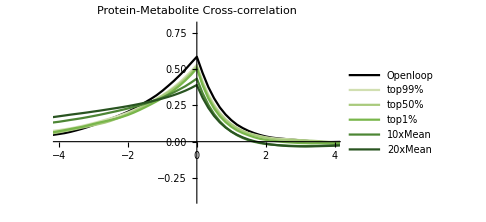

```mathematica
ListLinePlot[{ol500c24hmem[[6]],hmumem1[[6]],hmumem50[[6]],hmumem99[[6]],hmumem7000[[6]],hmumem14000[[6]]},PlotRange->{{-4,4},{-0.4,0.8}},PlotLegends->{"Openloop","top99%","top50%","top1%","10xMean","20xMean"},PlotLabel->Style["Protein-Metabolite Cross-correlation",Black,16],PlotStyle->{Directive[Black],Directive[RGBColor["#d1dfb1"],Thick],Directive[RGBColor["#a9ca7d"],Thick],Directive[RGBColor["#79b64b"],Thick],Directive[RGBColor["#4d8635"],Thick],Directive[RGBColor["#295421"],Thick]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

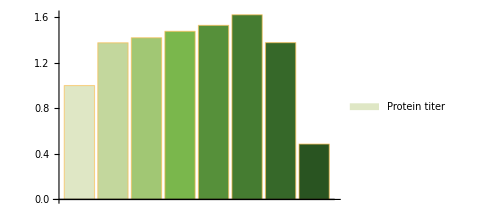

```mathematica
BarChart[{oltyp[[2]]/oltyp[[2]],hmutyp1[[2]]/oltyp[[2]],hmutyp10[[2]]/oltyp[[2]],hmutyp50[[2]]/oltyp[[2]],hmutyp90[[2]]/oltyp[[2]],hmutyp99[[2]]/oltyp[[2]],hmutyp7000[[2]]/oltyp[[2]],hmutyp14000[[2]]/oltyp[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#dfe7c5"],

RGBColor["#c3d79d"],

RGBColor["#a1c774"],

RGBColor["#7ab74c"],

RGBColor["#56903a"],
RGBColor["#457c31"],
RGBColor["#366829"],
RGBColor["#295421"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

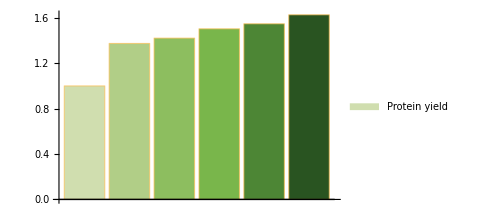

```mathematica
BarChart[{oltyp[[5]]/oltyp[[5]],hmutyp1[[5]]/oltyp[[5]],hmutyp10[[5]]/oltyp[[5]],hmutyp50[[5]]/oltyp[[5]],hmutyp90[[5]]/oltyp[[5]],hmutyp99[[5]]/oltyp[[5]]},ChartLegends->{"Protein yield"},ChartStyle->{RGBColor["#d0deaf"],
RGBColor["#b1ce87"],
RGBColor["#8dbe5f"],
RGBColor["#79b64b"],
RGBColor["#4d8635"],
RGBColor["#295421"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

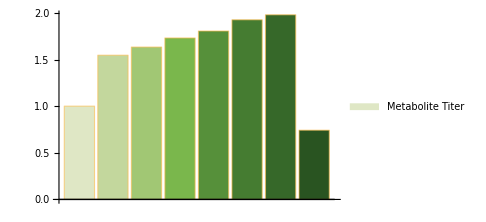

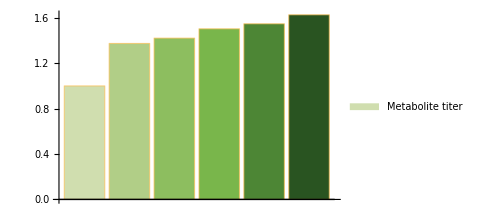

```mathematica
BarChart[{oltyp[[4]]/oltyp[[4]],hmutyp1[[4]]/oltyp[[4]],hmutyp10[[4]]/oltyp[[4]],hmutyp50[[4]]/oltyp[[4]],hmutyp90[[4]]/oltyp[[4]],hmutyp99[[4]]/oltyp[[4]],hmutyp7000[[4]]/oltyp[[4]],hmutyp14000[[4]]/oltyp[[4]]},ChartLegends->{"Metabolite Titer"},ChartStyle->{RGBColor["#dfe7c5"],

RGBColor["#c3d79d"],

RGBColor["#a1c774"],

RGBColor["#7ab74c"],

RGBColor["#56903a"],
RGBColor["#457c31"],
RGBColor["#366829"],
RGBColor["#295421"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
hmutyp7000=titeryieldproductivity[hmukill7000]
```

```mathematica
hmutyp14000=titeryieldproductivity[hmukill14000];
```

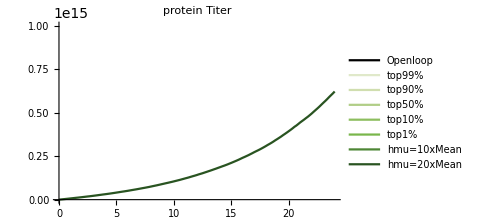

```mathematica
ListLinePlot[{oltyp[[1]],hmutyp1[[1]],hmutyp10[[1]],hmutyp50[[1]],hmutyp90[[1]],hmutyp99[[1]],hmutyp7000[[1]],hmutyp14000[[1]]},PlotLabel->"protein Titer",PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%","hmu=10xMean","hmu=20xMean"},PlotStyle->{Black,Lighter[RGBColor["#d0deaf"]],RGBColor["#d0deaf"],
RGBColor["#b1ce87"],
RGBColor["#8dbe5f"],
RGBColor["#79b64b"],
RGBColor["#4d8635"],
RGBColor["#295421"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
ListLinePlot[{oltyp[[3]],hmutyp1[[3]],hmutyp10[[3]],hmutyp50[[3]],hmutyp90[[3]],hmutyp99[[3]],hmutyp7000[[3]],hmutyp14000[[3]]},PlotLabel->"metabolite Titer",PlotLegends->{"Openloop","top99%","top90%","top50%","top10%","top1%","10xMean","20xMean"},PlotStyle->{Directive[Black,Thickness[0.01]],Directive[Lighter[RGBColor["#d0deaf"]],Thickness[0.01]],Directive[RGBColor["#d0deaf"],Thickness[0.01]],
Directive[RGBColor["#b1ce87"],Thickness[0.01]],
Directive[RGBColor["#8dbe5f"],Thickness[0.01]],
Directive[RGBColor["#79b64b"],Thickness[0.01]],
Directive[RGBColor["#4d8635"],Thickness[0.01]],
Directive[RGBColor["#295421"],Thickness[0.01]]},AxesStyle->Directive[Black, 16],ImageSize->Medium,PlotRange->{{0,24},{0,9*10^15}}]
```

-Graphics-

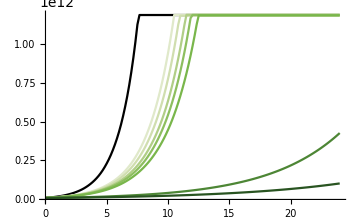

```mathematica
ListLinePlot[{Transpose@{ol500c24hkill[[All,1]],ol500c24hkill[[All,12]]},Transpose@{hmukill1[[All,1]],hmukill1[[All,12]]},Transpose@{hmukill10[[All,1]],hmukill10[[All,12]]},Transpose@{hmukill50[[All,1]],hmukill50[[All,12]]},Transpose@{hmukill90[[All,1]],hmukill90[[All,12]]},Transpose@{hmukill99[[All,1]],hmukill99[[All,12]]},Transpose@{hmukill7000[[All,1]],hmukill7000[[All,12]]},Transpose@{hmukill14000[[All,1]],hmukill14000[[All,12]]}},PlotStyle->{Black,Lighter[RGBColor["#d0deaf"]],RGBColor["#d0deaf"],
RGBColor["#b1ce87"],
RGBColor["#8dbe5f"],
RGBColor["#79b64b"],
RGBColor["#4d8635"],
RGBColor["#295421"]},AxesStyle->Directive[Black, 16],ImageSize->Medium, Axes->{True,True}]
```